```mathematica
DSolve[y''[x]-k y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(√k x) C[1]+ⅇ^(-√k x) C[2]}}

```mathematica
DSolve[{y''[x]-3 y[x]==0,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-√3 x) (1-C[1]+ⅇ^(2 √3 x) C[1])}}

```mathematica
DSolve[{y'[x]==x,y[0]==0},y[x],x]
```

{{y[x]→x^2/2}}

```mathematica
DSolve[{y'[x]==x,y[0]==0},y[x],x]
```

{{y[x]→x^2/2}}

```mathematica
DSolve[{y'[x]==x,y[0]==0,h'[x]==h[x],h[0]==1},{y[x],h[x]},x]
```

{{y[x]→x^2/2,h[x]→ⅇ^x}}

```mathematica
NIntegrate[2x,{x,0,4}]
```

16.

```mathematica
eqs={
y'[t]==y[t]+NIntegrate[2tt,{tt,0,a[t]}];
};

vars={y};
sol=NDSolve[eqs,vars,{t,0,6},StartingStepSize->0.001,Method->{"FixedStep",Method->"ExplicitEuler"}];
```

NIntegrate::nlim: tt = a[t] is not a valid limit of integration.

NDSolve::deqn: Equation or list of equations expected instead of Null in the first argument {Null}.

```mathematica
integral[x_Real,y_Real]:=NIntegrate[h[x,y+y2],{y2,x,y}];
NDSolve[{D[f[x,y],x]==integral[x,y],f[0,y]==0},f,{x,0,1},{y,0,1}]
```

NIntegrate::inumr: The integrand h[0.,0.0416667+y2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.0416667}}.

NIntegrate::inumr: The integrand h[0.,0.0833333+y2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.0833333}}.

NIntegrate::inumr: The integrand h[0.,0.125+y2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.125}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve[{f^(1,0)[x,y]==integral[x,y],f[0,y]==0},f,{x,0,1},{y,0,1}]

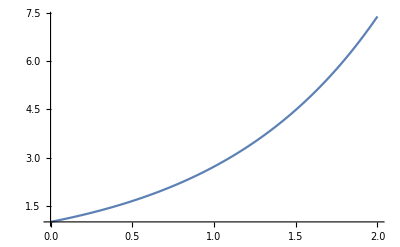

```mathematica
sol=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}];
Plot[y[x]/.sol,{x,0,2}]
```